```mathematica
Subscript[δ, a_,b_]:=KroneckerDelta[a,b]
Subscript[A, x_,a_]:=Subscript[δ, x,0] Subscript[δ, a,0]{{1,0},{0,0}}+Subscript[δ, x,0] Subscript[δ, a,1]{{0,0},{0,1}} + Subscript[δ, x,1] Subscript[δ, a,0](1/2*{{1,1},{1,1}})+Subscript[δ, x,1] Subscript[δ, a,1](1/2*{{1,-1},{-1,1}})
```

```mathematica
a_⊙b_:=KroneckerProduct[a,b]
Subscript[A2, x0_,x1_,a0_,a1_]:=Subscript[A, x0,a0]⊙ Subscript[A, x1,a1]
```

```mathematica
CC[i_,j_,k_,l_,q_]:=1/64(∑_(a=0)^1 ∑_(b=0)^1 (Subscript[δ, i,2a+b](∑_(x0=0)^1 ∑_(x1=0)^1 Subscript[A2, x0,x1,a,b])+Subscript[δ, j,2a+b](∑_(x0=0)^1 ∑_(x1=0)^1 Subscript[A2, x0,x1,a,BitXor[b,x1]])+Subscript[δ, k,2a+b](∑_(x0=0)^1 ∑_(x1=0)^1 Subscript[A2, x0,x1,BitXor[a,x0],b])+Subscript[δ, l,2a+b](∑_(x0=0)^1 ∑_(x1=0)^1 Subscript[A2, x0,x1,BitXor[a,x0],BitXor[b,x1]])))-q/16(4-Subscript[δ, i,4]-Subscript[δ, j,4]-Subscript[δ, k,4]-Subscript[δ, l,4])IdentityMatrix[4]
```

```mathematica
BC[q_]:=4*Max[Table[Eigenvalues[CC[i,j,k,l,q]],{i,0,4},{j,0,4},{k,0,4},{l,0,4}]];
```

```mathematica
η[q_]:=BC[q]/((1/2(1+1/(√2)))^2-q)
```

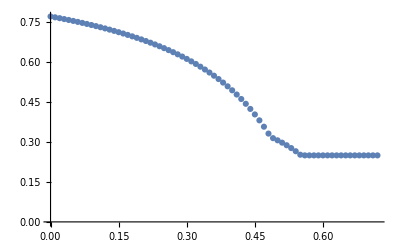

```mathematica
ListPlot[Monitor[Table[{q,η[q]},{q,0,(1/2(1+1/(√2)))^2,0.005}],Row[{ProgressIndicator[q,{0,(1/2(1+1/(√2)))^2}],q}," "]]]
```